## Белко Владислав, ПО-5

Лабораторная работа №5.

```mathematica
3*5
```

15

```mathematica
3 5
```

15

```mathematica
3      5
```

15

```mathematica
2 +    7
```

9

```mathematica
2/3
```

2/3

```mathematica
3     /7
```

3/7

```mathematica
17^(1/2)
```

√17

```mathematica
17.     ^(1/2)
```

4.12311

Задание 1.

а)Пробел выполняет роль знака умножения

```mathematica
4 2
```

8

б)Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
4      2
4      +2
4      -2
4       ^2
```

8

6

2

16

в)Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
47^(1/2)
4/7
```

√47

4/7

г)Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
47.^(1/2)
```

6.85565

д)Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
4 2 + 2
4 (2 + 2)
```

10

16

## Задание 2.

С помощью функции N вычислить √17 с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%] (*последнего числа*)
```

200.

Найти приближенное значение числа e^(Pi √163) с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа.

```mathematica
bv1=N[E^(Pi √163),40]
bv2=Round[N[E^(Pi √163),40]]
```

2.625374126407687439999999999992500725972×10^17

262537412640768744

```mathematica
bv3=bv2-bv1
```

7.499274028×10^-13

Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

Последовательно введите выражение

```mathematica
5>3
5<2
```

True

False

Справедливо ли неравенство

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E, 10]
N[E^Pi, 10]
```

22.45915772

23.14069263

## Задание 3.

Решить уравнения

```mathematica
NSolve[√(x+2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

Решить системы уравнений

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

Придумать свою

```mathematica
NSolve[{(2 x^2+2 y^2+2 y)/(y^2-4xy)==2, x^2 4y+2 y^2+4 x^2== 2}, {x,y}]
```

{{x→-1. √(1.-4. xy),y→-1.},{x→√(1.-4. xy),y→-1.},{x→-1. √(1.+4. xy),y→-1.-8. xy},{x→√(1.+4. xy),y→-1.-8. xy}}

## Задание 4.

```mathematica
FindRoot[x^4-8 x^2+3 == 2 x^3, {x, -2,1}]
```

{x→-1.8502}

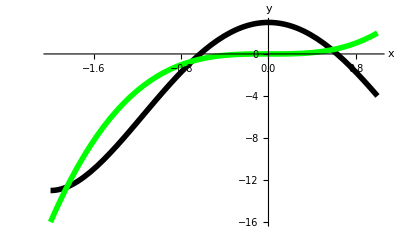

```mathematica
Plot[{x^4-8 x^2+3, 2 x^3}, {x, -2,1}, PlotStyle->{{Thickness[0.01], RGBColor[0,0,0]}, {Thickness[0.01], RGBColor[0,1,0]}}, AxesLabel->{"x", "y"}]
```

## Задание 5.

```mathematica
bv51=NDSolve[{y''[x]+x^2 y[x]-1==0, y[0]==0, y'[0]==1},y, {x,0,4}]
```

{{y→InterpolatingFunction[…]}}

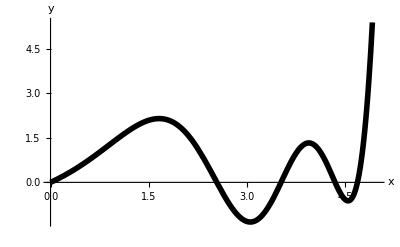

```mathematica
Plot[y[x]/.bv51, {x,0,5}, AxesLabel->{"x", "y"}, PlotStyle->{RGBColor[0,0,0], Thickness[0.01]}]
```

```mathematica
bv52=FindRoot[(y[x]/.bv51[[1]])==0, {x,2.6}]
```

{x→2.54324}

```mathematica
D[y[x]/.bv51[[1]],x]/.bv52
```

-4.08962

```mathematica
bv53 = FindRoot[D[y[x]/.bv51[[1]],x]==0, {x,3.2}]
```

{x→3.0556}

```mathematica
y[x]/.bv51[[1]]/.bv53
```

-1.33679

```mathematica
FindMinimum[y[x]/.bv51[[1]], {x,3.2}]
```

{-1.33679,{x→3.0556}}

## Задание 6.

```mathematica
task1 = Table[{x,(24+42x+12 x^2+4 x^3+2 x^4)(1+Random[Real, {-0.25,0.25}])}, {x,0,5,0.25}]
```

{{0.,24.9057},{0.25,40.5334},{0.5,37.8293},{0.75,49.4371},{1.,101.222},{1.25,105.985},{1.5,132.422},{1.75,191.543},{2.,203.712},{2.25,310.383},{2.5,262.007},{2.75,481.516},{3.,531.394},{3.25,534.95},{3.5,927.479},{3.75,806.152},{4.,1120.08},{4.25,1424.93},{4.5,1643.13},{4.75,1726.71},{5.,2803.51}}

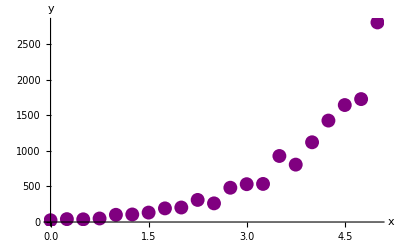

```mathematica
bvPlot1=ListPlot[task1, PlotStyle->{Purple,PointSize[0.025]}, AxesLabel->{"x", "y"}]
```

```mathematica
temp11=Fit[v1, {1,x,x^2, x^3, x^4},x]
```

45.0975-113.039 x+183.494 x^2-59.8767 x^3+9.44154 x^4

```mathematica
temp12=Fit[v1, {1,x,x^2, x^3, x^4},x]
```

45.0975-113.039 x+183.494 x^2-59.8767 x^3+9.44154 x^4

```mathematica
45.09750418398892-113.03852078340752 x+183.49432087017615 x^2-59.87669618744299 x^3+9.441537750078746 x^4
```

45.0975-113.039 x+183.494 x^2-59.8767 x^3+9.44154 x^4

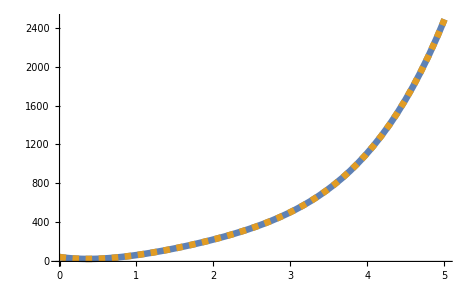

```mathematica
bvPlot2 =Plot[{temp11,temp12}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.01}]}}]
```

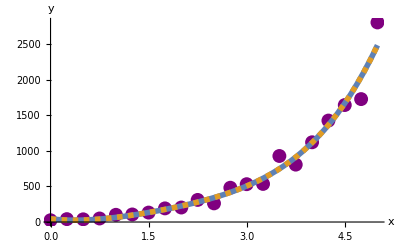

```mathematica
Show[bvPlot1,bvPlot2]
```

```mathematica
task2 = Table[{x,(24+42x+24Sin[x]+42Cos[x])(1+Random[Real, {-0.15, 0.15}])}, {x,0,5,0.25}]
```

{{0.,63.5284},{0.25,90.3507},{0.5,100.371},{0.75,102.486},{1.,111.126},{1.25,127.592},{1.5,98.6719},{1.75,113.164},{2.,104.753},{2.25,120.686},{2.5,93.8401},{2.75,116.89},{3.,103.841},{3.25,111.032},{3.5,129.712},{3.75,117.068},{4.,140.931},{4.25,160.29},{4.5,180.724},{4.75,195.368},{5.,227.844}}

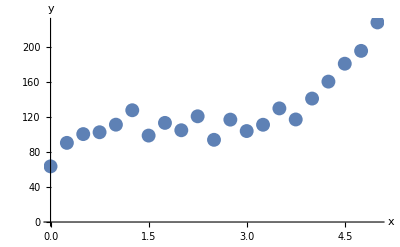

```mathematica
task2Plot=ListPlot[task2, PlotStyle->PointSize[0.025], AxesLabel->{"x", "y"}]
```

```mathematica
t21=Fit[task2, {1,x,Cos[x], Sin[x]},x]
```

22.081+42.5781 x+47.0197 Cos[x]+25.4977 Sin[x]

```mathematica
t22=Fit[task2, {1,x,x^2, x^3, x^4},x]
```

66.4521+90.2298 x-56.1902 x^2+12.2719 x^3-0.672818 x^4

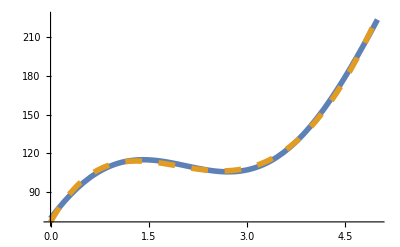

```mathematica
plot2 =Plot[{t21,t22}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

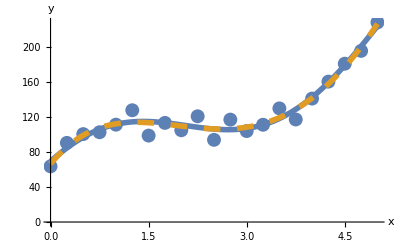

```mathematica
Show[task2Plot, plot2]
```